# Visualizing the H’ for 135Pr

## H’ in terms of energy ellipses as function of the polar coordinates.

#### Author: Robert Poenaru Email: robert.poenaru@drd.unibuc.ro

## Defining an ellipse

## Using ContourPlot

```mathematica
ellipseEq[a_,b_]:=ContourPlot[x^2/a^2+y^2/b^2==1,{x,-a,a},{y,-b,b},PlotRange->Automatic,AspectRatio->Automatic];
```

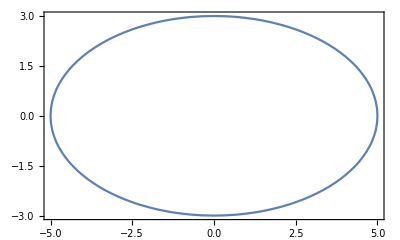

```mathematica
ellipseEq[5,3]
```

## Using Solve eq

```mathematica
sols[a_,b_]:=y/.Solve[x^2/a^2+y^2/b^2==1,y];
ellipseSolve[a_,b_]:=Plot[y/.Solve[x^2/a^2+y^2/b^2==1,y],{x,-1.1a,1.1a},AspectRatio->Automatic];
```

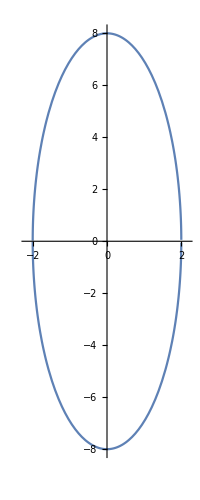

```mathematica
ellipseSolve[2,8]
```

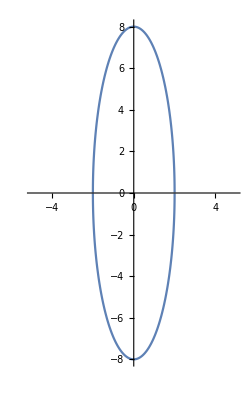

```mathematica
Plot[Sequence@@sols[2,8],{x,-5,5},AspectRatio->Automatic]
```